```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
datafull=Import["../data/CGL_num.csv",HeaderLines->2];
datafull[[1]]
Dimensions@datafull
```

{3616,4,280110,17130421-02000,7,26,0,680,750,750,700,462.778,144.207,144.207,0.3,1044,1.92,2004.48,24.008,1525.99,152.861,154.39,0.542195,207037,0.300134,0,29-DEC-17 01.22.39.000000000 PM -06:00}

{44963,27}

```mathematica
nullpos=Position[datafull[[All,17]],_?(Head@#==String&)];
datafull=Delete[datafull,nullpos];
```

```mathematica
(* mostlyzeropos=Position[datafull[[All,9]],_?(#==0&)][[{2,3}]];
datafull=Delete[datafull,mostlyzeropos]; *)
```

```mathematica
deletepos=Position[datafull[[All,17]],_?(1200<#&)];
datafull=Delete[datafull,deletepos];
```

```mathematica
deletepos2=Position[datafull[[All,16]],_?(80000<#&)];
datafull=Delete[datafull,deletepos2];
```

```mathematica
deletepos3=Position[datafull[[All,16]],_?(200>#&)];
datafull=Delete[datafull,deletepos3];
```

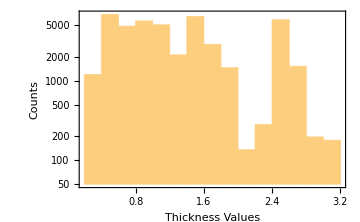
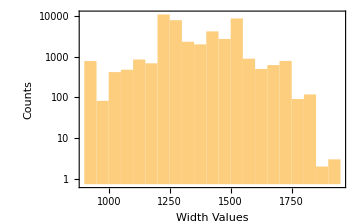

```mathematica
{Histogram[datafull[[All,17]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,16]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
density[thick_,width_,length_,weight_]:=N@weight/(thick*width*length);
```

```mathematica
thickvaluesthkpos=datafull[[All,17]];
widthvaluesthkpos=datafull[[All,16]];
lengthvaluesthkpos=datafull[[All,20]];
weightvaluesthkpos=datafull[[All,19]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
KeySort@Counts@densities
```

<|-0.00686112→1,-0.00463997→1,-0.00209751→1,-0.00135243→1,-0.000638687→1,43602,0.00164515→1,0.00205702→1,0.00218787→1,0.00246979→1,0.00249878→1|>
 |  |  |  |

```mathematica
datafull=datafull[[Flatten@Position[densities,_?(6.5*10^(-6)<#<8.5*10^(-6)&)]]];
```

```mathematica
datafull=Delete[datafull,Position[datafull[[All,27]],_?(#==""&)]];
```

```mathematica
thickvaluesthkpos=datafull[[All,17]];
widthvaluesthkpos=datafull[[All,16]];
lengthvaluesthkpos=datafull[[All,20]];
weightvaluesthkpos=datafull[[All,19]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
```

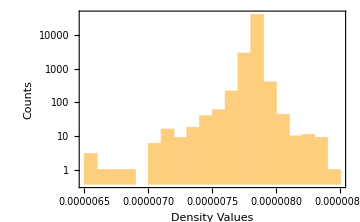

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
Length@datafull
```

44711

```mathematica
timecolumn=Table[{StringDrop[datafull[[i,27]],-7],Which[StringDrop[datafull[[i,27]],{1,32}]=="-06:00",-4,StringDrop[datafull[[i,27]],{1,32}]=="-05:00",-3]},{i,Length@datafull}]
```

{{29-DEC-17 01.22.39.000000000 PM,-4},{29-DEC-17 01.38.09.000000000 PM,-4},{29-DEC-17 01.50.48.000000000 PM,-4},44705,{02-NOV-20 07.03.32.000000000 AM,-4},{02-NOV-20 07.19.39.000000000 AM,-4},{02-NOV-20 07.34.19.000000000 AM,-4}}
 |  |  |  |

```mathematica
timecolumnconvert=Table[TimeZoneConvert[DateObject[StringReplacePart[i[[1]],":",{{13,13},{16,16}}],TimeZone->i[[2]]],$TimeZone],{i,timecolumn}]
```

{Fri 29 Dec 2017 19:22:39GMT+2,Fri 29 Dec 2017 19:38:09GMT+2,Fri 29 Dec 2017 19:50:48GMT+2,Sat 30 Dec 2017 00:08:02GMT+2,44704,Mon 2 Nov 2020 13:03:32GMT+2,Mon 2 Nov 2020 13:19:39GMT+2,Mon 2 Nov 2020 13:34:19GMT+2}
 |  |  |  |

```mathematica
timecolumnseconds=Table[AbsoluteTime@i,{i,timecolumnconvert}]
```

{3723564159,3723565089,3723565848,3723581282,3723582508,3723583636,3723584720,3723585812,3723586896,3723587988,3723589059,3723590138,44687,3813300701,3813301701,3813302824,3813303932,3813305046,3813307201,3813308278,3813309160,3813310095,3813311012,3813311979,3813312859}
 |  |  |  |

```mathematica
datafull=Join[datafull,Partition[timecolumnseconds,1],2];
```

```mathematica
datafullsorted=Sort[datafull,#1[[28]]<#2[[28]]&];
```

```mathematica
differences=N[Differences[datafullsorted[[All,28]]]/60]
```

{15.5,12.65,257.233,20.4333,18.8,18.0667,18.2,18.0667,18.2,44692,18.4667,18.5667,35.9167,17.95,14.7,15.5833,15.2833,16.1167,14.6667}
 |  |  |  |

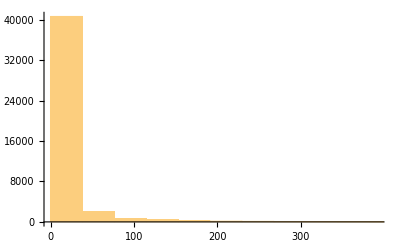

```mathematica
Histogram[differences]
```

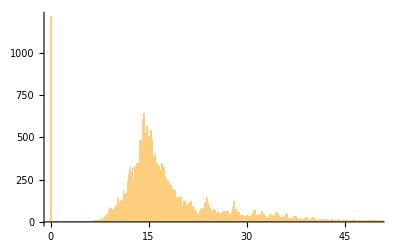

```mathematica
Histogram[differences,{10^-1}]
```

```mathematica
Length@Position[differences,_?(#<38.23&)]
(Length@datafullsorted)-Length@Position[differences,_?(#<38.23&)]
```

40654

4057

```mathematica
(* trial={1,2,3,10,11,12,13,20,21,22,29,30,31,38,45};Differences@trial;
pos=Flatten@Position[Differences@trial,_?(#≥7&)]
seq=Table[ConstantArray[i[[1]],i[[2]]],{i,MapThread[{#1,#2}&,{Range[Length@pos+1],Flatten@{First@pos,Table[{pos[[i+1]]-pos[[i]]},{i,Length@pos-1}],Length@trial-Last@pos}}]}]
Length@Flatten@seq
Length@trial *)
```

```mathematica
pos=Flatten@Position[differences,_?(#≥38.23&)];
sequencecolumn=Flatten@Table[ConstantArray[i[[1]],i[[2]]],{i,MapThread[{#1,#2}&,{Range[Length@pos+1],Flatten@{First@pos,Table[{pos[[i+1]]-pos[[i]]},{i,Length@pos-1}],Length@datafullsorted-Last@pos}}]}];
```

```mathematica
Length@sequencecolumn
Length@DeleteDuplicates@sequencecolumn
Length@datafullsorted
```

44711

4057

44711

```mathematica
datafullsorted=Join[Partition[Range@Length@datafullsorted,1],Partition[sequencecolumn,1],datafullsorted,2];
```

```mathematica
(* checking if sequences are revealing consecutive *)
Length@Table[DeleteDuplicates@i,{i,Split[datafullsorted[[All,1]],#2==#1&]}]
Length@DeleteDuplicates[datafullsorted[[All,1]]]
```

44711

44711

```mathematica
datafullsorted[[1000]]
```

{1000,123,4089,8,344314,18016001-05000,8,26,0.7,680,750,750,700,462.778,144.207,144.207,0.5,1591,1.25,1988.75,18.818,1205.56,148.913,148.716,0.499934,207962,0.497644,1,09-FEB-18 05.39.44.000000000 AM -06:00,3727165184}

```mathematica
data=Join[datafullsorted[[All,{1,2}]],ConstantArray[{0,0,0,0,0,0},Length@datafullsorted],datafullsorted[[All,{18,19,29,30}]],2]
```

{{1,1,0,0,0,0,0,0,1044,1.92,29-DEC-17 01.22.39.000000000 PM -06:00,3723564159},{2,1,0,0,0,0,0,0,1229,1.9761,29-DEC-17 01.38.09.000000000 PM -06:00,3723565089},44708,{44711,4057,0,0,0,0,0,0,1426.07,0.736646,02-NOV-20 07.34.19.000000000 AM -06:00,3813312859}}
 |  |  |  |

```mathematica
Dimensions@data
```

{44711,12}

```mathematica
(* Export["cgl_manipulated_44711.csv",data] *)
```